## fun with Groebner basis

### Ideal membership problem

```mathematica
GroebnerBasis[{x z-y^2,x^3-z^2},{x,y,z},MonomialOrder->DegreeLexicographic]
```

{-y^2+x z,x^3-z^2,x^2 y^2-z^3,x y^4-z^4,y^6-z^5}

```mathematica
PolynomialReduce[-4 x^2 y^2 z^2+y^6+3 z^5,{-y^2+x z,x^3-z^2,x^2 y^2-z^3,x y^4-z^4,y^6-z^5},{x,y,z}]
```

{{-4 y^4-4 x y^2 z,0,0,0,-3},0}

```mathematica
PolynomialReduce[xy-5 z^2+x,{-y^2+x z,x^3-z^2,x^2 y^2-z^3,x y^4-z^4,y^6-z^5},{x,y,z}]
```

{{0,0,0,0,0},x+xy-5 z^2}

### solve polynomial equations

```mathematica
GroebnerBasis[{x^2+y^2+z^2-1,x^2+z^2-y,x-z},{x,y,z},MonomialOrder->Lexicographic]
```

{-1+2 z^2+4 z^4,y-2 z^2,x-z}

### Implicitization problem

```mathematica
GroebnerBasis[{x-t^4,y-t^3,z-t^2},{t,x,y,z},MonomialOrder->Lexicographic]
```

{y^2-z^3,x-z^2,-y+t z,t y-z^2,t^2-z}

```mathematica
GroebnerBasis[{x-t-u,y-t^2-2t u,z-t^3-3 t^2 u},{t,u,x,y,z},MonomialOrder->Lexicographic]
```

{-3 x^2 y^2+4 y^3+4 x^3 z-6 x y z+z^2,2 u y^3+x y^3-4 x^2 y z+5 y^2 z-2 u z^2-2 x z^2,-2 u y^2-x y^2+2 u x z+2 x^2 z-y z,u x y-x^2 y+2 y^2-u z-x z,2 u x^2-2 x^3-2 u y+3 x y-z,u^2-x^2+y,t+u-x}

```mathematica
GroebnerBasis[{x y-1,x z-1},{x,y,z},MonomialOrder->Lexicographic]
```

{y-z,-1+x z}

```mathematica
GroebnerBasis[{(y-z)x^2+x y-1,(y-z)x^2+x z-1},{x,y,z},MonomialOrder->Lexicographic]
```

{y-z,-1+x z}

```mathematica
GroebnerBasis[{v x-u^2,u y-v^2,z-u},{u,v,x,y,z},MonomialOrder->Lexicographic]
```

{x^2 y z-z^4,-x y z+v z^2,v x-z^2,v^2-y z,u-z}

```mathematica
GroebnerBasis[{v x-u^2,u y-v^2,z-u,1-u v w},{u,v,w,x,y,z},MonomialOrder->Lexicographic]
```

{x^2 y-z^3,-x+w z^3,-1+w x y,v-w y z^2,u-z}

```mathematica
GroebnerBasis[{(x-t)^2+(y-t^2)^2-4,-2(x-t)-4t(y-t^2)},{t,x,y},MonomialOrder->Lexicographic]//MatrixForm
```

(-1156+688 x^2-191 x^4+16 x^6+544 y+30 x^2 y-40 x^4 y+225 y^2-96 x^2 y^2+16 x^4 y^2-136 y^3-32 x^2 y^3+16 y^4
7327 t+6929 x-2946 x^3+224 x^5-1928 t y+2922 x y-1480 x^3 y+128 x^5 y-768 t y^2-792 x y^2-224 x^3 y^2-896 t y^3-544 x y^3+128 x^3 y^3+256 t y^4-384 x y^4
-952-431 t x+159 x^2+16 x^4-320 y+12 t x y+214 x^2 y-32 x^4 y+366 y^2+48 t x y^2+32 x^2 y^2+80 y^3+64 t x y^3-32 x^2 y^3-32 y^4
-697 t-23 x+288 t x^2+174 x^3-32 x^5-108 t y-322 x y+112 x^3 y+336 t y^2-32 x y^2-32 x^3 y^2-64 t y^3+96 x y^3
-128+135 t^2+26 t x+111 x^2-16 x^4+64 y+40 t x y+8 x^2 y+32 y^2+32 t x y^2-16 x^2 y^2-16 y^3)

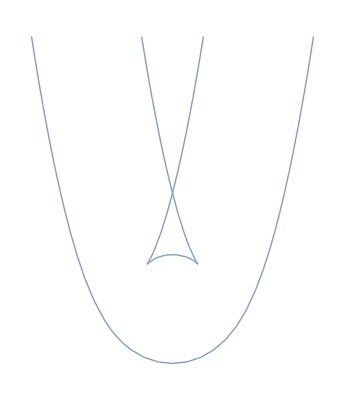

```mathematica
Region[ImplicitRegion[-1156+688 x^2-191 x^4+16 x^6+544 y+30 x^2 y-40 x^4 y+225 y^2-96 x^2 y^2+16 x^4 y^2-136 y^3-32 x^2 y^3+16 y^4==0,{{x,-6,6},{y,-2,10}}]]
```

## rusultant

```mathematica
Resultant[x y-1,x^2+y^2-4,x]
```

1-4 y^2+y^4

## radical membership

```mathematica
GroebnerBasis[{x y^2+2y^2,x^4-2x^2+1},{x,y,z},MonomialOrder->Lexicographic]
```

{y^2,1-2 x^2+x^4}

```mathematica
Solve[x y^2+2y^2==0&&x^4-2x^2+1==0,{x,y}]
```

{{x→-1,y→0},{x→1,y→0}}

```mathematica
GroebnerBasis[{x y^2+2y^2,x^4-2x^2+1,1-z(y-x^2+1)},{x,y,z},MonomialOrder->Lexicographic]
```

{1}

## intersection of ideals

```mathematica
GroebnerBasis[{t x^2y,(1-t)x y^2},{t,x,y},MonomialOrder->Lexicographic]
```

{x^2 y^2,-x y^2+t x y^2,t x^2 y}

```mathematica
GroebnerBasis[{t(x+y)^4(x^2+y)^2(x-5y),(1-t)(x+y)(x^2+y)^3(x+3y)},{t,x,y},MonomialOrder->Lexicographic][[1]]//FullSimplify
```

```mathematica
Variables[(x-5 y) (x+y)^4 (x^2+y)^3 (x+3 y)/y]
```

{x,y}

```mathematica
Do[MemberQ[Variables[GroebnerBasis[{t(x+y)^4(x^2+y)^2(x-5y),(1-t)(x+y)(x^2+y)^3(x+3y)},{t,x,y},MonomialOrder->Lexicographic][[i]]],t]//Print,{i,5}]
```

False

True

True

True

«1 more identical outputs»

```mathematica
Module[{test},
test=GroebnerBasis[{t(x+y)^4(x^2+y)^2(x-5y),(1-t)(x+y)(x^2+y)^3(x+3y)},{t,x,y},MonomialOrder->Lexicographic];
(*Print[FullSimplify[test]];*)
Do[If[!MemberQ[Variables[GroebnerBasis[{t(x+y)^4(x^2+y)^2(x-5y),(1-t)(x+y)(x^2+y)^3(x+3y)},{t,x,y},MonomialOrder->Lexicographic][[i]]],t],Print[test[[i]]//FullSimplify]],{i,Length[test]}]]
```

(x-5 y) (x+y)^4 (x^2+y)^3 (x+3 y)

## problem 1

```mathematica
Get["/Users/jsw/Documents/Courses/topics_in_modern_QFT/hw2/4pt_twistor_jsw.wl"]
```

## reproduce results of the example given in the lecture

### solution I

```mathematica
xx=-AA[4,3]/AA[1,3];yy=-BB[1,4]/BB[2,4];
```

```mathematica
mp[v[xx λ[1],λt[4]],(2mp[P[[1]],P[[2]]]+2mp[P[[1]],P[[4]]])/(2mp[P[[1]],P[[2]]])AA[4,3]/AA[1,3] v[λ[1],λt[4]]+AA[1,3]/AA[4,3] v[λ[4],λt[1]]]//FullSimplify
```

x2/2

```mathematica
2mp[P[[1]],P[[2]]]//FullSimplify
```

x1

```mathematica
2mp[P[[1]],P[[4]]]//FullSimplify
```

x2

```mathematica
(-BB[1,4]AA[1,2] BB[3,4]^3 AA[1,4])/(xx yy BB[2,3]BB[2,4])xx//FullSimplify
```

x1^2 x2^2

```mathematica
ⅈ (2mp[P[[1]],P[[2]]])( 2mp[P[[1]],P[[4]]] )(ⅈ AA[1,2]^4)/(AA[1,2]AA[2,3]AA[3,4]AA[4,1])//FullSimplify
```

x1^2 x2^2

### solution II

```mathematica
xx=(-(x1)AA[1,3])/((x1+x2)AA[3,4]);yy=(-(x2)AA[1,3])/((x1+x2)AA[2,3]);
ⅈ xx AA[1,4] (ⅈ BB[1,2])/yy(ⅈ AA[4,2])/(AA[2,3]AA[3,4])ⅈ xx^3 BB[1,4]//FullSimplify
```

(x1^4 x2^4)/(x1+x2)^2

```mathematica
mp[v[xx λ[4],λt[1]],(2mp[P[[1]],P[[2]]]+2mp[P[[1]],P[[4]]])/(2mp[P[[1]],P[[2]]])AA[4,3]/AA[1,3] v[λ[1],λt[4]]+AA[1,3]/AA[4,3] v[λ[4],λt[1]]]//FullSimplify
```

-x2/2

## problem 1

### solution I

```mathematica
xx=(-AA[4,3])/AA[1,3];yy=(-BB[1,4])/BB[2,4];
-ⅈ BB[1,4]/xx((-ⅈ AA[1,2])/yy)ⅈ BB[2,3]^3/(BB[3,4]BB[2,4])(-ⅈ xx AA[1,4])//FullSimplify
```

x1^2 x2^2

```mathematica
ⅈ (2mp[P[[1]],P[[2]]])( 2mp[P[[1]],P[[4]]] )(ⅈ BB[2,3]^4)/(BB[1,2]BB[2,3]BB[3,4]BB[4,1])//FullSimplify
```

x1^2 x2^2

```mathematica
mp[v[xx λ[1],λt[4]],(2P[[1]].P[[2]]+2P[[1]].P[[4]])/(2P[[1]].P[[2]])AA[4,3]/AA[1,3] v[λ[1],λt[4]]+AA[1,3]/AA[4,3] v[λ[4],λt[1]]]//FullSimplify
```

x2/2

### solution II

```mathematica
xx=(-(x1)AA[1,3])/((x1+x2)AA[3,4]);yy=(-(x2)AA[1,3])/((x1+x2)AA[2,3]);
ⅈ xx AA[1,4]ⅈ yy^3 BB[1,2](-ⅈ AA[2,4]^3/(AA[2,3]AA[3,4]))ⅈ BB[1,4]/xx//FullSimplify
```

x1^2 x2^2

```mathematica
mp[v[xx λ[4],λt[1]],(2P[[1]].P[[2]]+2P[[1]].P[[4]])/(2P[[1]].P[[2]])AA[4,3]/AA[1,3] v[λ[1],λt[4]]+AA[1,3]/AA[4,3] v[λ[4],λt[1]]]//FullSimplify
```

-x2/2

## problem 2

```mathematica
Quit[]
```

```mathematica
f1 = y^2-x^3-1;
f2 = x^2+2y^2-1;
Ideal={f1,f2};
```

```mathematica
sol=Solve[Ideal==0,{x,y,z}]
```

{{x→-1,y→0},{x→1/4 (1-ⅈ √7),y→-√(1/2 (1-1/16 (1-ⅈ √7)^2))},{x→1/4 (1-ⅈ √7),y→√(1/2 (1-1/16 (1-ⅈ √7)^2))},{x→1/4 (1+ⅈ √7),y→-√(1/2 (1-1/16 (1+ⅈ √7)^2))},{x→1/4 (1+ⅈ √7),y→√(1/2 (1-1/16 (1+ⅈ √7)^2))}}

```mathematica
sol//Length
```

5

```mathematica
gr=GroebnerBasis[Ideal,{x,y,z},MonomialOrder->DegreeReverseLexicographic]
LeadingTerms=MonomialList[#,{x,y,z},DegreeReverseLexicographic][[1]]&/@%
```

{-1+x^2+2 y^2,-1-x+y^2+2 x y^2,1+x-7 y^2+8 y^4}

{x^2,2 x y^2,8 y^4}

```mathematica
{1,x,x*y,y,y^2,y^3}  (* Monomials which are NOT divided by any LeadingTerm *)
Basis=MonomialList[Total[%],{x,y,z},DegreeReverseLexicographic]//Reverse  (* Sort the monomials from lower to higher *)
Do[PolynomialReduce[Basis[[i]],gr,{x,y,z},MonomialOrder->DegreeReverseLexicographic]//Print,{i,Length[Basis]}]
```

{1,x,x y,y,y^2,y^3}

{1,y,x,y^2,x y,y^3}

{{0,0,0},1}

{{0,0,0},y}

{{0,0,0},x}

{{0,0,0},y^2}

{{0,0,0},x y}

{{0,0,0},y^3}

```mathematica
Do[Block[{var={x,y,z},ref=Total[Basis]},MonomialList[PolynomialReduce[x*Basis[[j]],gr,var,MonomialOrder->DegreeReverseLexicographic][[2]]+ref,var,DegreeReverseLexicographic]]//Length//Print,{j,Length[Basis]}]
```

6

6

6

«3 more identical outputs»

```mathematica
CompanionMatrix[F_,Gr_,var_,basis_]:=Module[{i,j,ref,AuxVar,matrix,NN},
	ref=AuxVar*Total[basis];
	NN=Length[basis];
matrix=Table[MonomialList[PolynomialReduce[F*basis[[j]],Gr,var,MonomialOrder->DegreeReverseLexicographic][[2]]+ref,var,DegreeReverseLexicographic]//Reverse,{j,1,NN}];
	Return[Transpose[matrix]/.AuxVar->0/.(#->1&/@var)];
]
```

```mathematica
Mx=CompanionMatrix[x,gr,{x,y,z},Basis];
My=CompanionMatrix[y,gr,{x,y,z},Basis];
```

```mathematica
N[Total[(x^3+y^3)/.sol],30]
```

-2.25+0. ⅈ

```mathematica
sol1=Append[sol,{x->-1,y->0}]
```

{{x→-1,y→0},{x→1/4 (1-ⅈ √7),y→-√(1/2 (1-1/16 (1-ⅈ √7)^2))},{x→1/4 (1-ⅈ √7),y→√(1/2 (1-1/16 (1-ⅈ √7)^2))},{x→1/4 (1+ⅈ √7),y→-√(1/2 (1-1/16 (1+ⅈ √7)^2))},{x→1/4 (1+ⅈ √7),y→√(1/2 (1-1/16 (1+ⅈ √7)^2))},{x→-1,y→0}}

```mathematica
Total[(x^3+y^3)/.sol1]//FullSimplify
```

-13/4

```mathematica
(Mx.Mx.Mx+My.My.My)//MatrixForm
```

(-1 | -1/8 | 1/2 | -1/8 | 5/16 | -11/64
0 | -1 | 1/2 | -1/8 | 1/2 | -1/8
0 | -1/8 | -1/2 | -1/8 | 5/16 | -11/64
1 | 7/8 | -1/2 | -1/8 | -3/16 | 45/64
0 | 0 | 1/2 | -1/8 | -1/2 | -1/8
1 | 1 | -1/2 | 7/8 | -1/2 | -1/8)

```mathematica
(Mx.Mx.Mx+My.My.My)//Tr
N[%,30]
```

-13/4

-3.25

## problem 3

```mathematica
Quit[]
```

```mathematica
GroebnerBasis[{x^2+y^2+z^2-1,x y z-3,z^3-x^2-2y},{y,z,x},MonomialOrder->Lexicographic,CoefficientDomain->RationalFunctions]
```

{729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16,84119067+153757926 x+94791654 x^2+6428196 x^3-6487968 x^4+25662818 x^5+12411837 x^6-12629132 x^7-4562358 x^8-190354 x^9-771207 x^10-732870 x^11-434487 x^12+410626 x^13-142332 x^14+131486 x^15+2296350 z,13798998+21051009 x+13735926 x^2+2447559 x^3-1406352 x^4+3492182 x^5+1639998 x^6-1510973 x^7-906882 x^8+49199 x^9-159198 x^10-55575 x^11-95448 x^12+76924 x^13-26718 x^14+20309 x^15+2296350 y}

```mathematica
{729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16,84119067+153757926 x+94791654 x^2+6428196 x^3-6487968 x^4+25662818 x^5+12411837 x^6-12629132 x^7-4562358 x^8-190354 x^9-771207 x^10-732870 x^11-434487 x^12+410626 x^13-142332 x^14+131486 x^15+2296350 z,13798998+21051009 x+13735926 x^2+2447559 x^3-1406352 x^4+3492182 x^5+1639998 x^6-1510973 x^7-906882 x^8+49199 x^9-159198 x^10-55575 x^11-95448 x^12+76924 x^13-26718 x^14+20309 x^15+2296350 y}//Length
```

3

```mathematica
Module[{test},
test=GroebnerBasis[{x^2+y^2+z^2-1,x y z-3,z^3-x^2-2y},{y,z,x},MonomialOrder->Lexicographic,CoefficientDomain->RationalFunctions];
Do[If[!MemberQ[Variables[test[[i]]],y],If[!MemberQ[Variables[test[[i]]],z],Print[test[[i]]]]],{i,Length[test]}]]
```

729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16

## another way

```mathematica
GroebnerBasis[{x^2+y^2+z^2-1,x y z-3,z^3-x^2-2y},{z,y,x},MonomialOrder->Lexicographic,CoefficientDomain->RationalFunctions]
```

{729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16,13798998+21051009 x+13735926 x^2+2447559 x^3-1406352 x^4+3492182 x^5+1639998 x^6-1510973 x^7-906882 x^8+49199 x^9-159198 x^10-55575 x^11-95448 x^12+76924 x^13-26718 x^14+20309 x^15+2296350 y,84119067+153757926 x+94791654 x^2+6428196 x^3-6487968 x^4+25662818 x^5+12411837 x^6-12629132 x^7-4562358 x^8-190354 x^9-771207 x^10-732870 x^11-434487 x^12+410626 x^13-142332 x^14+131486 x^15+2296350 z}

```mathematica
{729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16,84119067+153757926 x+94791654 x^2+6428196 x^3-6487968 x^4+25662818 x^5+12411837 x^6-12629132 x^7-4562358 x^8-190354 x^9-771207 x^10-732870 x^11-434487 x^12+410626 x^13-142332 x^14+131486 x^15+2296350 z,13798998+21051009 x+13735926 x^2+2447559 x^3-1406352 x^4+3492182 x^5+1639998 x^6-1510973 x^7-906882 x^8+49199 x^9-159198 x^10-55575 x^11-95448 x^12+76924 x^13-26718 x^14+20309 x^15+2296350 y}//Length
```

3

```mathematica
Module[{test},
test=GroebnerBasis[{x^2+y^2+z^2-1,x y z-3,z^3-x^2-2y},{z,y,x},MonomialOrder->Lexicographic,CoefficientDomain->RationalFunctions];
Do[If[!MemberQ[Variables[test[[i]]],y],If[!MemberQ[Variables[test[[i]]],z],Print[test[[i]]]]],{i,Length[test]}]]
```

729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16

729+1944 x+1944 x^2+756 x^3+168 x^5+292 x^6-12 x^7-133 x^8-36 x^9-8 x^10-12 x^11-9 x^12+2 x^14+x^16

### both z y x and y z x gives the same result, as expected.